```mathematica
g=9.8; (*grav. constant*)
V = 30.;
th = 50. * π/ 180.;
y0=1.; (*20 degrees*)
yprime0 = V Sin[th]; (*starting from rest*)
x0 = 1.;
xprime0=V Cos[th];
vt = 100.;
ode1={x''[t] == (-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t] ^ 2]};
ode2 ={y''[t]==-g (1+(y'[t] / vt ^ 2) Sqrt[x'[t]^2+y'[t]^2])};
sol=NDSolve[{ode1, ode2,y[0]==y0, y'[0]==yprime0,x[0]==x0,x'[0]==xprime0},{y, x},{t,0,200}]
```

{{y→InterpolatingFunction[{{0.,200.}},<>],x→InterpolatingFunction[{{0.,200.}},<>]}}

```mathematica
myplot1 = ParametricPlot[ Evaluate[{x[t],y[t]}/.sol],{t,0,200},PlotStyle-> RGBColor[0,0,1],PlotRange-> {{0,100},{0,100}}];
```

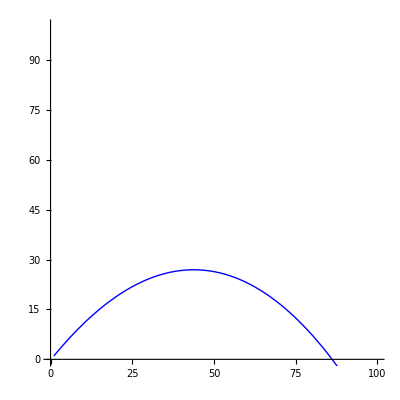

```mathematica
Show[{myplot1}]
```

```mathematica
Manipulate[
Module[
{result = NDSolve[{x''[t] == (-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t] ^ 2],y''[t]==-g (1+(y'[t] / vt ^ 2) Sqrt[x'[t]^2+y'[t]^2]),{x[0]==0,y[0]==y0},{x'[0]==V Cos[th],y'[0]==V Sin[th]}},{x, y},{t,0,200}]},
ParametricPlot[ {Evaluate[{x[t],y[t]}/.result],{V Cos[th] t, y0 + V Sin[th] t - 0.5 g t^2}},{t,0,tf},PlotRange-> {{0,150},{0,150}},AxesLabel->{"x (m)","y (m)"},ImageSize->{500,300}]],
{{y0, 0, "initial height (m)"}, 0, 100, Appearance -> "Labeled"},
{{V,10,"initial velocity (m/s)"},10,200,Appearance->"Labeled"},
{{vt,10,"terminal velocity (m/s)"},10,200,Appearance->"Labeled"},
{{th,45*Pi/180,"angle (rad)"},0.,Pi/2,Appearance->"Labeled"},
{{tf, 0.01,"time (s)"},0.01,20.,Appearance->"Labeled"}]
```

```mathematica
Manipulate[
Module[
{result = With[{vt=Sqrt[2 m 9.8/(0.5 1.29 A)]},NDSolve[{x''[t] == (-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t] ^ 2],y''[t]==-g (1+(y'[t] / vt ^ 2) Sqrt[x'[t]^2+y'[t]^2]),{x[0]==0,y[0]==y0},{x'[0]==V Cos[th],y'[0]==V Sin[th]}},{x, y},{t,0,200}]]},
ParametricPlot[ {Evaluate[{x[t],y[t]}/.result],{V Cos[th] t, y0 + V Sin[th] t - 0.5 g t^2}},{t,0,tf},PlotRange-> {{0,150},{0,150}},AxesLabel->{"x (m)","y (m)"},ImageSize->{500,300}]],
{{A, 0.001, "Area (m^2)"}, 0.001, 1, Appearance -> "Labeled"},
{{m, 0.01, "Mass (kg)"}, 0.01, 3, Appearance -> "Labeled"},
{{y0, 0, "initial height (m)"}, 0, 100, Appearance -> "Labeled"},
{{V,10,"initial velocity (m/s)"},10,200,Appearance->"Labeled"},
{{vt,10,"terminal velocity (m/s)"},10,200,Appearance->"Labeled"},
{{th,45*Pi/180,"angle (rad)"},0.,Pi/2,Appearance->"Labeled"},
{{tf, 0.01,"time (s)"},0.01,20.,Appearance->"Labeled"}]
```